```mathematica
dir="D:\\workingBuffer 2";
```

```mathematica
dir="D:\\betterEnergy 2";
```

```mathematica
indexOfEgg=6;
```

```mathematica
GetNumberOfOrganisms[frameNo_]:=Module[{path,file,headings,applyHeading,items,nOrganisms,nFertile},
path = StringForm["``\\output\\frame``.csv",dir,frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
nOrganisms="o"/.items//CountDistinct;
nFertile=Cases[{"o","ct"}/.items,{x_,indexOfEgg}->x]//CountDistinct;
{nOrganisms,nFertile}
]
```

```mathematica
f0=10;
fMax=2845620;
df=10000;
GetNumberOfOrganisms[fMax]//Print;
frames=Table[f,{f,f0,fMax,df}];
nOrgsList=ParallelMap[GetNumberOfOrganisms,frames]//Transpose;
```

{2,2}

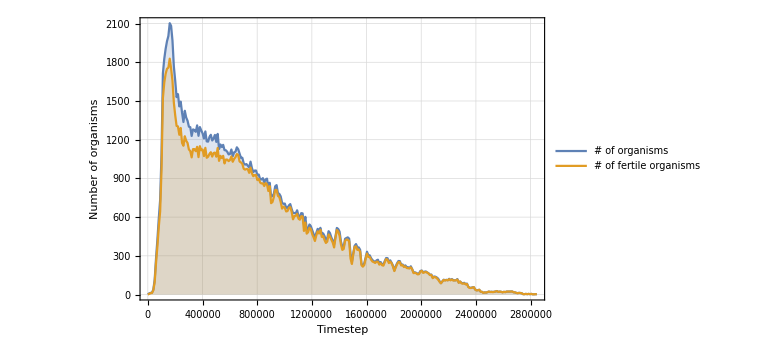

```mathematica
plot=ListPlot[
nOrgsList,
DataRange->{f0,fMax},
Filling->Bottom,
Joined->True,
PlotRange->Full,
Frame->{{True,False},{True,False}},
FrameLabel->{"Timestep","Number of organisms"},
PlotLegends->Placed[{"# of organisms","# of fertile organisms"},Above],
ImageSize->Large,
GridLines->Automatic
]
```

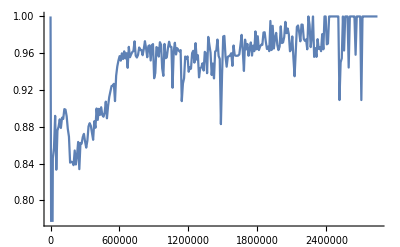

```mathematica
ListLinePlot[(#⟦2⟧)/(#⟦1⟧)&/@Transpose[nOrgsList],DataRange->{f0,fMax}]
```